```mathematica
description="Slepton-side photon radiation";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
MakeBoxes[p1, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(1\)]\)";
MakeBoxes[p2, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(2\)]\)";
MakeBoxes[k1, TraditionalForm] := "\!\(\*SubscriptBox[\(k\),\(1\)]\)"; 
MakeBoxes[k2, TraditionalForm] := "\!\(\*SubscriptBox[\(k\),\(2\)]\)";
```

### Get amplitudes

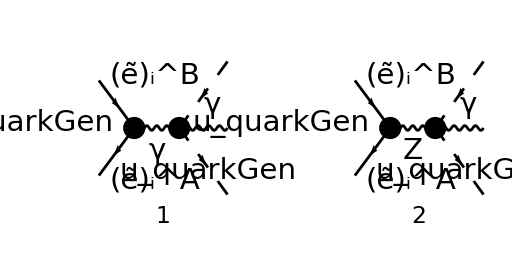

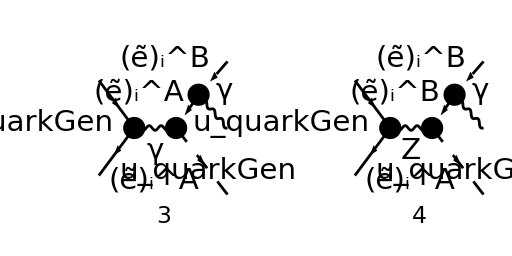

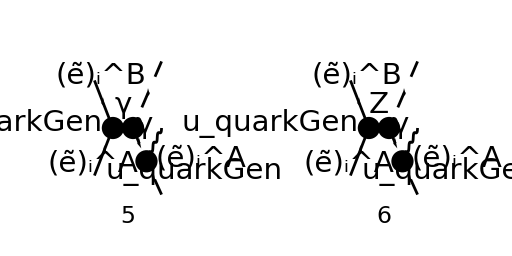

```mathematica
diags[0]=InsertFields[
CreateTopologies[0,2->3],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],V[1],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{S[1],S[2],S[3],S[4],F[3]}
(*F[3] to get rid of diagrams with quark-side radiation*)
];
Paint[
diags[0],
ColumnsXRows->{2,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

```mathematica
Mlist[0]=FCFAConvert[
CreateFeynAmp[diags[0]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k,k2},
ChangeDimension->D,
UndoChiralSplittings->True,
List->True,
LorentzIndexNames->{μ,ν,ρ},
Contract->True,
DropSumOver->True,
SMP->True
]/.{MQU[quarkGen]->0}
```

{-(4 e^3 δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·ε^*(k)).(φ(p_1)))/(3 (k+k_1+k_2)^2),(ⅈ e^2 (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (φ(-p_2)).((2 ⅈ e δ_Col1Col2 (sin(θ_W)) (γ·ε^*(k)).(γ̄)^6)/(3 (cos(θ_W)))+(ⅈ e δ_Col1Col2 (4 (sin(θ_W))^2-3) (γ·ε^*(k)).(γ̄)^7)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)))/((cos(θ_W)) (sin(θ_W)) ((k+k_1+k_2)^2-m_Z^2)),-(2 e^3 δ_Col1Col2 IndexDelta(A,B) (-(k·ε^*(k))-2 (k_1·ε^*(k))) (φ(-p_2)).(γ·(k+k_1-k_2)).(φ(p_1)))/(3 (k+k_1+k_2)^2 ((-k-k_1)^2-(MSf(A,2,i))^2)),(ⅈ e^2 (-(k·ε^*(k))-2 (k_1·ε^*(k))) (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (φ(-p_2)).((2 ⅈ e δ_Col1Col2 (sin(θ_W)) (γ·(k+k_1-k_2)).(γ̄)^6)/(3 (cos(θ_W)))+(ⅈ e δ_Col1Col2 (4 (sin(θ_W))^2-3) (γ·(k+k_1-k_2)).(γ̄)^7)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)))/(2 (cos(θ_W)) (sin(θ_W)) ((-k-k_1)^2-(MSf(B,2,i))^2) ((k+k_1+k_2)^2-m_Z^2)),-(2 e^3 δ_Col1Col2 IndexDelta(A,B) (-(k·ε^*(k))-2 (k_2·ε^*(k))) (φ(-p_2)).(γ·(k-k_1+k_2)).(φ(p_1)))/(3 (k+k_1+k_2)^2 ((k+k_2)^2-(MSf(A,2,i))^2)),(ⅈ e^2 (-(k·ε^*(k))-2 (k_2·ε^*(k))) (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (φ(-p_2)).((2 ⅈ e δ_Col1Col2 (sin(θ_W)) (γ·(k-k_1+k_2)).(γ̄)^6)/(3 (cos(θ_W)))+(ⅈ e δ_Col1Col2 (4 (sin(θ_W))^2-3) (γ·(k-k_1+k_2)).(γ̄)^7)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)))/(2 (cos(θ_W)) (sin(θ_W)) ((k+k_2)^2-(MSf(A,2,i))^2) ((k+k_1+k_2)^2-m_Z^2))}

Change  to for quark charge in photon diagram.

### Simplify amplitudes

```mathematica
Mγ[0]=Total[Mlist[0][[{1,3,5}]]] 3/2 SMP["e_Q"]//Simplify
```

1/(k+k_1+k_2)^2 e^3 e_Q δ_Col1Col2 IndexDelta(A,B) (((k·ε^*(k)+2 (k_1·ε^*(k))) (φ(-p_2)).(γ·(k+k_1-k_2)).(φ(p_1)))/((-k-k_1)^2-(MSf(A,2,i))^2)+((k·ε^*(k)+2 (k_2·ε^*(k))) (φ(-p_2)).(γ·(k-k_1+k_2)).(φ(p_1)))/((k+k_2)^2-(MSf(A,2,i))^2)-2 (φ(-p_2)).(γ·ε^*(k)).(φ(p_1)))

Change slepton propagator in B-radiation diagram to match that of the Z-diagrams (the slepton masses can be interchanged in the photon diagram because of the Kronecker-delta)

```mathematica
Mγ[1]=Mγ[0]/.{
FeynAmpDenominator[PropagatorDenominator[Momentum[-k-k1,D],MSf[A,2,i]]]->FeynAmpDenominator[PropagatorDenominator[Momentum[-k-k1,D],MSf[B,2,i]]]}
```

1/(k+k_1+k_2)^2 e^3 e_Q δ_Col1Col2 IndexDelta(A,B) (((k·ε^*(k)+2 (k_2·ε^*(k))) (φ(-p_2)).(γ·(k-k_1+k_2)).(φ(p_1)))/((k+k_2)^2-(MSf(A,2,i))^2)+((k·ε^*(k)+2 (k_1·ε^*(k))) (φ(-p_2)).(γ·(k+k_1-k_2)).(φ(p_1)))/((-k-k_1)^2-(MSf(B,2,i))^2)-2 (φ(-p_2)).(γ·ε^*(k)).(φ(p_1)))

Substitute for Cγ for easier comparison to my notes.

```mathematica
Mγ[2]=Mγ[1]/.{SMP["e"]^3SMP["e_Q"]IndexDelta[A,B]FeynAmpDenominator[PropagatorDenominator[Momentum[k+k1+k2,D],0]]->Cγ}
```

Cγ δ_Col1Col2 (((k·ε^*(k)+2 (k_2·ε^*(k))) (φ(-p_2)).(γ·(k-k_1+k_2)).(φ(p_1)))/((k+k_2)^2-(MSf(A,2,i))^2)+((k·ε^*(k)+2 (k_1·ε^*(k))) (φ(-p_2)).(γ·(k+k_1-k_2)).(φ(p_1)))/((-k-k_1)^2-(MSf(B,2,i))^2)-2 (φ(-p_2)).(γ·ε^*(k)).(φ(p_1)))

Simplify Z diagrams by writing them in terms of Zql, Zqr and ZliAB

```mathematica
MZ[0]=Total[Mlist[0][[{2,4,6}]]];
MZ[1]=MZ[0]/.{4 SMP["sin_W"]^2-3:>12 Zql};
MZ[2]=MZ[1]/.{SMP["sin_W"]/SMP["cos_W"]:>3 Zqr / (SMP["sin_W"] SMP["cos_W"])};
MZ[3]=MZ[2]//.{USf[2,i][A,2] Conjugate[USf[2,i][B,2]]:>KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]}//Simplify;
MZ[4]=MZ[3]//.{2SMP["sin_W"]^2 KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]->-2 ZliAB}
```

-((ⅈ e^2 ZliAB (-((k·ε^*(k)+2 (k_2·ε^*(k))) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(k-k_1+k_2)).(γ̄)^7+Zqr (γ·(k-k_1+k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/((k+k_2)^2-(MSf(A,2,i))^2)-((k·ε^*(k)+2 (k_1·ε^*(k))) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(k+k_1-k_2)).(γ̄)^7+Zqr (γ·(k+k_1-k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/((-k-k_1)^2-(MSf(B,2,i))^2)+2 (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·ε^*(k)).(γ̄)^7+Zqr (γ·ε^*(k)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1))))/((cos(θ_W)) (sin(θ_W)) ((k+k_1+k_2)^2-m_Z^2)))

Substitute for CZ for easier comparison to my notes.

```mathematica
MZ[5]=MZ[4]/.{SMP["e"]^2 ZliAB FeynAmpDenominator[PropagatorDenominator[Momentum[k+k1+k2,D],SMP["m_Z"]]]->CZ SMP["sin_W"]^2SMP["cos_W"]^2/SMP["e"]}
```

-1/e ⅈ CZ (cos(θ_W)) (sin(θ_W)) (-((k·ε^*(k)+2 (k_2·ε^*(k))) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(k-k_1+k_2)).(γ̄)^7+Zqr (γ·(k-k_1+k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/((k+k_2)^2-(MSf(A,2,i))^2)-((k·ε^*(k)+2 (k_1·ε^*(k))) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(k+k_1-k_2)).(γ̄)^7+Zqr (γ·(k+k_1-k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/((-k-k_1)^2-(MSf(B,2,i))^2)+2 (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·ε^*(k)).(γ̄)^7+Zqr (γ·ε^*(k)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))

```mathematica
M[0]=Mγ[2]+MZ[5]
```

Cγ δ_Col1Col2 (((k·ε^*(k)+2 (k_2·ε^*(k))) (φ(-p_2)).(γ·(k-k_1+k_2)).(φ(p_1)))/((k+k_2)^2-(MSf(A,2,i))^2)+((k·ε^*(k)+2 (k_1·ε^*(k))) (φ(-p_2)).(γ·(k+k_1-k_2)).(φ(p_1)))/((-k-k_1)^2-(MSf(B,2,i))^2)-2 (φ(-p_2)).(γ·ε^*(k)).(φ(p_1)))-1/e ⅈ CZ (cos(θ_W)) (sin(θ_W)) (-((k·ε^*(k)+2 (k_2·ε^*(k))) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(k-k_1+k_2)).(γ̄)^7+Zqr (γ·(k-k_1+k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/((k+k_2)^2-(MSf(A,2,i))^2)-((k·ε^*(k)+2 (k_1·ε^*(k))) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(k+k_1-k_2)).(γ̄)^7+Zqr (γ·(k+k_1-k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/((-k-k_1)^2-(MSf(B,2,i))^2)+2 (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·ε^*(k)).(γ̄)^7+Zqr (γ·ε^*(k)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))

```mathematica
M[1]=M[0]/.{Pair[Momentum[k,D],Momentum[Polarization[k,-I],D]]->0}
```

Cγ δ_Col1Col2 ((2 (k_2·ε^*(k)) (φ(-p_2)).(γ·(k-k_1+k_2)).(φ(p_1)))/((k+k_2)^2-(MSf(A,2,i))^2)+(2 (k_1·ε^*(k)) (φ(-p_2)).(γ·(k+k_1-k_2)).(φ(p_1)))/((-k-k_1)^2-(MSf(B,2,i))^2)-2 (φ(-p_2)).(γ·ε^*(k)).(φ(p_1)))-1/e ⅈ CZ (cos(θ_W)) (sin(θ_W)) (-(2 (k_2·ε^*(k)) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(k-k_1+k_2)).(γ̄)^7+Zqr (γ·(k-k_1+k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/((k+k_2)^2-(MSf(A,2,i))^2)-(2 (k_1·ε^*(k)) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(k+k_1-k_2)).(γ̄)^7+Zqr (γ·(k+k_1-k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/((-k-k_1)^2-(MSf(B,2,i))^2)+2 (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·ε^*(k)).(γ̄)^7+Zqr (γ·ε^*(k)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))

Impose momentum conservation  for further simplification using the Dirac equation.

```mathematica
M[2]=M[1]/.{
Momentum[k+k2-k1,D]->Momentum[p1+p2-2k1,D],
Momentum[k+k1-k2,D]->Momentum[p1+p2-2k2,D]
}
```

Cγ δ_Col1Col2 ((2 (k_2·ε^*(k)) (φ(-p_2)).(γ·(-2 k_1+p_1+p_2)).(φ(p_1)))/((k+k_2)^2-(MSf(A,2,i))^2)+(2 (k_1·ε^*(k)) (φ(-p_2)).(γ·(-2 k_2+p_1+p_2)).(φ(p_1)))/((-k-k_1)^2-(MSf(B,2,i))^2)-2 (φ(-p_2)).(γ·ε^*(k)).(φ(p_1)))-1/e ⅈ CZ (cos(θ_W)) (sin(θ_W)) (-(2 (k_2·ε^*(k)) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(-2 k_1+p_1+p_2)).(γ̄)^7+Zqr (γ·(-2 k_1+p_1+p_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/((k+k_2)^2-(MSf(A,2,i))^2)-(2 (k_1·ε^*(k)) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(-2 k_2+p_1+p_2)).(γ̄)^7+Zqr (γ·(-2 k_2+p_1+p_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/((-k-k_1)^2-(MSf(B,2,i))^2)+2 (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·ε^*(k)).(γ̄)^7+Zqr (γ·ε^*(k)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))

```mathematica
M[3]=M[2]//DiracSimplify//Simplify
```

2 δ_Col1Col2 ((4 CZ Zql (k_2·ε^*(k)) (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)))/((k+k_2)^2-(MSf(A,2,i))^2)+(4 CZ Zqr (k_2·ε^*(k)) (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)))/((k+k_2)^2-(MSf(A,2,i))^2)+(4 CZ Zql (k_1·ε^*(k)) (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)))/((k+k_1)^2-(MSf(B,2,i))^2)+(4 CZ Zqr (k_1·ε^*(k)) (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)))/((k+k_1)^2-(MSf(B,2,i))^2)+2 CZ Zql (φ(-p_2)).(γ·ε^*(k)).(γ̄)^7.(φ(p_1))+2 CZ Zqr (φ(-p_2)).(γ·ε^*(k)).(γ̄)^6.(φ(p_1))-(2 Cγ (k_2·ε^*(k)) (φ(-p_2)).(γ·k_1).(φ(p_1)))/((k+k_2)^2-(MSf(A,2,i))^2)-(2 Cγ (k_1·ε^*(k)) (φ(-p_2)).(γ·k_2).(φ(p_1)))/((k+k_1)^2-(MSf(B,2,i))^2)-Cγ (φ(-p_2)).(γ·ε^*(k)).(φ(p_1)))

### Square the amplitude

```mathematica
FCClearScalarProducts[];
SPD[p1]=SPD[p2]=SPD[k]=0;
SPD[k1]=MSf[B,2,i]^2;
SPD[k2]=MSf[A,2,i]^2;
```

```mathematica
MCC[0]=ComplexConjugate[M[3],Conjugate->{CZ}]
```

(8 Zql Conjugate[CZ] δ_Col1Col2 (k_2·ε(k)) (φ(p_1)).(γ̄)^6.(γ·k_1).(φ(-p_2)))/((k+k_2)^2-(MSf(A,2,i))^2)+(8 Zqr Conjugate[CZ] δ_Col1Col2 (k_2·ε(k)) (φ(p_1)).(γ̄)^7.(γ·k_1).(φ(-p_2)))/((k+k_2)^2-(MSf(A,2,i))^2)+(8 Zql Conjugate[CZ] δ_Col1Col2 (k_1·ε(k)) (φ(p_1)).(γ̄)^6.(γ·k_2).(φ(-p_2)))/((k+k_1)^2-(MSf(B,2,i))^2)+(8 Zqr Conjugate[CZ] δ_Col1Col2 (k_1·ε(k)) (φ(p_1)).(γ̄)^7.(γ·k_2).(φ(-p_2)))/((k+k_1)^2-(MSf(B,2,i))^2)+4 Zql Conjugate[CZ] δ_Col1Col2 (φ(p_1)).(γ̄)^6.(γ·ε(k)).(φ(-p_2))+4 Zqr Conjugate[CZ] δ_Col1Col2 (φ(p_1)).(γ̄)^7.(γ·ε(k)).(φ(-p_2))-(4 Cγ δ_Col1Col2 (k_2·ε(k)) (φ(p_1)).(γ·k_1).(φ(-p_2)))/((k+k_2)^2-(MSf(A,2,i))^2)-(4 Cγ δ_Col1Col2 (k_1·ε(k)) (φ(p_1)).(γ·k_2).(φ(-p_2)))/((k+k_1)^2-(MSf(B,2,i))^2)-2 Cγ δ_Col1Col2 (φ(p_1)).(γ·ε(k)).(φ(-p_2))

```mathematica
Msquared[0]=(M[3] MCC[0])//FeynAmpDenominatorExplicit//FermionSpinSum[#,ExtraFactor->1/(4 SUNN^2)]&//SUNSimplify[#,SUNNToCACF->False]&//DoPolarizationSums[#,k,0]&//DiracSimplify[#,DiracTraceEvaluate->True]&
```

-(8 (MSf(A,2,i))^2 (k_1·p_1) (k_1·p_2) Cγ^2)/(N (k·k_2)^2)-(8 (k_1·k_2) (k_1·p_2) (k_2·p_1) Cγ^2)/(N (k·k_1) (k·k_2))-(8 (k_1·p_2) (k_2·p_1) Cγ^2)/(N (k·k_1))-(8 (k_1·p_2) (k_2·p_1) Cγ^2)/(N (k·k_2))-(8 (k_1·k_2) (k_1·p_1) (k_2·p_2) Cγ^2)/(N (k·k_1) (k·k_2))-(8 (k_1·p_1) (k_2·p_2) Cγ^2)/(N (k·k_1))-(8 (k_1·p_1) (k_2·p_2) Cγ^2)/(N (k·k_2))-(8 (MSf(B,2,i))^2 (k_2·p_1) (k_2·p_2) Cγ^2)/(N (k·k_1)^2)+(8 (k_1·k_2)^2 (p_1·p_2) Cγ^2)/(N (k·k_1) (k·k_2))+(8 (k_1·k_2) (p_1·p_2) Cγ^2)/(N (k·k_1))+(8 (k_1·k_2) (p_1·p_2) Cγ^2)/(N (k·k_2))+(4 D (p_1·p_2) Cγ^2)/N-(8 (p_1·p_2) Cγ^2)/N+(4 (MSf(A,2,i))^2 (MSf(B,2,i))^2 (p_1·p_2) Cγ^2)/(N (k·k_1)^2)+(4 (MSf(A,2,i))^2 (MSf(B,2,i))^2 (p_1·p_2) Cγ^2)/(N (k·k_2)^2)+(Zql Conjugate[CZ] tr((γ·k_1).(γ·p_2).(γ·k_2).(γ·p_1).(γ̄)^5) (k_1·k_2) Cγ)/(N (k·k_1) (k·k_2))-(Zqr Conjugate[CZ] tr((γ·k_1).(γ·p_2).(γ·k_2).(γ·p_1).(γ̄)^5) (k_1·k_2) Cγ)/(N (k·k_1) (k·k_2))+(Zql Conjugate[CZ] tr((γ·k_2).(γ·p_2).(γ·k_1).(γ·p_1).(γ̄)^5) (k_1·k_2) Cγ)/(N (k·k_1) (k·k_2))-(Zqr Conjugate[CZ] tr((γ·k_2).(γ·p_2).(γ·k_1).(γ·p_1).(γ̄)^5) (k_1·k_2) Cγ)/(N (k·k_1) (k·k_2))-(CZ Zql tr((γ·p_1).(γ·k_1).(γ·p_2).(γ·k_2).(γ̄)^5) (k_1·k_2) Cγ)/(N (k·k_1) (k·k_2))+(CZ Zqr tr((γ·p_1).(γ·k_1).(γ·p_2).(γ·k_2).(γ̄)^5) (k_1·k_2) Cγ)/(N (k·k_1) (k·k_2))-(CZ Zql tr((γ·p_1).(γ·k_2).(γ·p_2).(γ·k_1).(γ̄)^5) (k_1·k_2) Cγ)/(N (k·k_1) (k·k_2))+(CZ Zqr tr((γ·p_1).(γ·k_2).(γ·p_2).(γ·k_1).(γ̄)^5) (k_1·k_2) Cγ)/(N (k·k_1) (k·k_2))+(8 CZ Zql (MSf(A,2,i))^2 (k_1·p_1) (k_1·p_2) Cγ)/(N (k·k_2)^2)+(8 CZ Zqr (MSf(A,2,i))^2 (k_1·p_1) (k_1·p_2) Cγ)/(N (k·k_2)^2)+(8 Zql Conjugate[CZ] (MSf(A,2,i))^2 (k_1·p_1) (k_1·p_2) Cγ)/(N (k·k_2)^2)+(8 Zqr Conjugate[CZ] (MSf(A,2,i))^2 (k_1·p_1) (k_1·p_2) Cγ)/(N (k·k_2)^2)+(8 CZ Zql (k_1·k_2) (k_1·p_2) (k_2·p_1) Cγ)/(N (k·k_1) (k·k_2))+(8 CZ Zqr (k_1·k_2) (k_1·p_2) (k_2·p_1) Cγ)/(N (k·k_1) (k·k_2))+(8 Zql Conjugate[CZ] (k_1·k_2) (k_1·p_2) (k_2·p_1) Cγ)/(N (k·k_1) (k·k_2))+(8 Zqr Conjugate[CZ] (k_1·k_2) (k_1·p_2) (k_2·p_1) Cγ)/(N (k·k_1) (k·k_2))+(8 CZ Zql (k_1·p_2) (k_2·p_1) Cγ)/(N (k·k_1))+(8 CZ Zqr (k_1·p_2) (k_2·p_1) Cγ)/(N (k·k_1))+(8 Zql Conjugate[CZ] (k_1·p_2) (k_2·p_1) Cγ)/(N (k·k_1))+(8 Zqr Conjugate[CZ] (k_1·p_2) (k_2·p_1) Cγ)/(N (k·k_1))+(8 CZ Zql (k_1·p_2) (k_2·p_1) Cγ)/(N (k·k_2))+(8 CZ Zqr (k_1·p_2) (k_2·p_1) Cγ)/(N (k·k_2))+(8 Zql Conjugate[CZ] (k_1·p_2) (k_2·p_1) Cγ)/(N (k·k_2))+(8 Zqr Conjugate[CZ] (k_1·p_2) (k_2·p_1) Cγ)/(N (k·k_2))+(8 CZ Zql (k_1·k_2) (k_1·p_1) (k_2·p_2) Cγ)/(N (k·k_1) (k·k_2))+(8 CZ Zqr (k_1·k_2) (k_1·p_1) (k_2·p_2) Cγ)/(N (k·k_1) (k·k_2))+(8 Zql Conjugate[CZ] (k_1·k_2) (k_1·p_1) (k_2·p_2) Cγ)/(N (k·k_1) (k·k_2))+(8 Zqr Conjugate[CZ] (k_1·k_2) (k_1·p_1) (k_2·p_2) Cγ)/(N (k·k_1) (k·k_2))+(8 CZ Zql (k_1·p_1) (k_2·p_2) Cγ)/(N (k·k_1))+(8 CZ Zqr (k_1·p_1) (k_2·p_2) Cγ)/(N (k·k_1))+(8 Zql Conjugate[CZ] (k_1·p_1) (k_2·p_2) Cγ)/(N (k·k_1))+(8 Zqr Conjugate[CZ] (k_1·p_1) (k_2·p_2) Cγ)/(N (k·k_1))+(8 CZ Zql (k_1·p_1) (k_2·p_2) Cγ)/(N (k·k_2))+(8 CZ Zqr (k_1·p_1) (k_2·p_2) Cγ)/(N (k·k_2))+(8 Zql Conjugate[CZ] (k_1·p_1) (k_2·p_2) Cγ)/(N (k·k_2))+(8 Zqr Conjugate[CZ] (k_1·p_1) (k_2·p_2) Cγ)/(N (k·k_2))+(8 CZ Zql (MSf(B,2,i))^2 (k_2·p_1) (k_2·p_2) Cγ)/(N (k·k_1)^2)+(8 CZ Zqr (MSf(B,2,i))^2 (k_2·p_1) (k_2·p_2) Cγ)/(N (k·k_1)^2)+(8 Zql Conjugate[CZ] (MSf(B,2,i))^2 (k_2·p_1) (k_2·p_2) Cγ)/(N (k·k_1)^2)+(8 Zqr Conjugate[CZ] (MSf(B,2,i))^2 (k_2·p_1) (k_2·p_2) Cγ)/(N (k·k_1)^2)-(8 CZ Zql (k_1·k_2)^2 (p_1·p_2) Cγ)/(N (k·k_1) (k·k_2))-(8 CZ Zqr (k_1·k_2)^2 (p_1·p_2) Cγ)/(N (k·k_1) (k·k_2))-(8 Zql Conjugate[CZ] (k_1·k_2)^2 (p_1·p_2) Cγ)/(N (k·k_1) (k·k_2))-(8 Zqr Conjugate[CZ] (k_1·k_2)^2 (p_1·p_2) Cγ)/(N (k·k_1) (k·k_2))+(8 CZ Zql (p_1·p_2) Cγ)/N-(4 CZ D Zql (p_1·p_2) Cγ)/N+(8 CZ Zqr (p_1·p_2) Cγ)/N-(4 CZ D Zqr (p_1·p_2) Cγ)/N-(4 D Zql Conjugate[CZ] (p_1·p_2) Cγ)/N+(8 Zql Conjugate[CZ] (p_1·p_2) Cγ)/N-(4 D Zqr Conjugate[CZ] (p_1·p_2) Cγ)/N+(8 Zqr Conjugate[CZ] (p_1·p_2) Cγ)/N-(8 CZ Zql (k_1·k_2) (p_1·p_2) Cγ)/(N (k·k_1))-(8 CZ Zqr (k_1·k_2) (p_1·p_2) Cγ)/(N (k·k_1))-(8 Zql Conjugate[CZ] (k_1·k_2) (p_1·p_2) Cγ)/(N (k·k_1))-(8 Zqr Conjugate[CZ] (k_1·k_2) (p_1·p_2) Cγ)/(N (k·k_1))-(8 CZ Zql (k_1·k_2) (p_1·p_2) Cγ)/(N (k·k_2))-(8 CZ Zqr (k_1·k_2) (p_1·p_2) Cγ)/(N (k·k_2))-(8 Zql Conjugate[CZ] (k_1·k_2) (p_1·p_2) Cγ)/(N (k·k_2))-(8 Zqr Conjugate[CZ] (k_1·k_2) (p_1·p_2) Cγ)/(N (k·k_2))-(4 CZ Zql (MSf(A,2,i))^2 (MSf(B,2,i))^2 (p_1·p_2) Cγ)/(N (k·k_1)^2)-(4 CZ Zqr (MSf(A,2,i))^2 (MSf(B,2,i))^2 (p_1·p_2) Cγ)/(N (k·k_1)^2)-(4 Zql Conjugate[CZ] (MSf(A,2,i))^2 (MSf(B,2,i))^2 (p_1·p_2) Cγ)/(N (k·k_1)^2)-(4 Zqr Conjugate[CZ] (MSf(A,2,i))^2 (MSf(B,2,i))^2 (p_1·p_2) Cγ)/(N (k·k_1)^2)-(4 CZ Zql (MSf(A,2,i))^2 (MSf(B,2,i))^2 (p_1·p_2) Cγ)/(N (k·k_2)^2)-(4 CZ Zqr (MSf(A,2,i))^2 (MSf(B,2,i))^2 (p_1·p_2) Cγ)/(N (k·k_2)^2)-(4 Zql Conjugate[CZ] (MSf(A,2,i))^2 (MSf(B,2,i))^2 (p_1·p_2) Cγ)/(N (k·k_2)^2)-(4 Zqr Conjugate[CZ] (MSf(A,2,i))^2 (MSf(B,2,i))^2 (p_1·p_2) Cγ)/(N (k·k_2)^2)+(Zql Conjugate[CZ] tr((γ·k_1).(γ·p_2).(γ·k_2).(γ·p_1).(γ̄)^5) Cγ)/(N (k·k_1))-(Zqr Conjugate[CZ] tr((γ·k_1).(γ·p_2).(γ·k_2).(γ·p_1).(γ̄)^5) Cγ)/(N (k·k_1))+(Zql Conjugate[CZ] tr((γ·k_2).(γ·p_2).(γ·k_1).(γ·p_1).(γ̄)^5) Cγ)/(N (k·k_1))-(Zqr Conjugate[CZ] tr((γ·k_2).(γ·p_2).(γ·k_1).(γ·p_1).(γ̄)^5) Cγ)/(N (k·k_1))-(CZ Zql tr((γ·p_1).(γ·k_1).(γ·p_2).(γ·k_2).(γ̄)^5) Cγ)/(N (k·k_1))+(CZ Zqr tr((γ·p_1).(γ·k_1).(γ·p_2).(γ·k_2).(γ̄)^5) Cγ)/(N (k·k_1))-(CZ Zql tr((γ·p_1).(γ·k_2).(γ·p_2).(γ·k_1).(γ̄)^5) Cγ)/(N (k·k_1))+(CZ Zqr tr((γ·p_1).(γ·k_2).(γ·p_2).(γ·k_1).(γ̄)^5) Cγ)/(N (k·k_1))+(Zql Conjugate[CZ] tr((γ·k_1).(γ·p_2).(γ·k_2).(γ·p_1).(γ̄)^5) Cγ)/(N (k·k_2))-(Zqr Conjugate[CZ] tr((γ·k_1).(γ·p_2).(γ·k_2).(γ·p_1).(γ̄)^5) Cγ)/(N (k·k_2))+(Zql Conjugate[CZ] tr((γ·k_2).(γ·p_2).(γ·k_1).(γ·p_1).(γ̄)^5) Cγ)/(N (k·k_2))-(Zqr Conjugate[CZ] tr((γ·k_2).(γ·p_2).(γ·k_1).(γ·p_1).(γ̄)^5) Cγ)/(N (k·k_2))-(CZ Zql tr((γ·p_1).(γ·k_1).(γ·p_2).(γ·k_2).(γ̄)^5) Cγ)/(N (k·k_2))+(CZ Zqr tr((γ·p_1).(γ·k_1).(γ·p_2).(γ·k_2).(γ̄)^5) Cγ)/(N (k·k_2))-(CZ Zql tr((γ·p_1).(γ·k_2).(γ·p_2).(γ·k_1).(γ̄)^5) Cγ)/(N (k·k_2))+(CZ Zqr tr((γ·p_1).(γ·k_2).(γ·p_2).(γ·k_1).(γ̄)^5) Cγ)/(N (k·k_2))+(2 CZ Zql^2 Conjugate[CZ] tr((γ·p_1).(γ·k_1).(γ·p_2).(γ·k_2).(γ̄)^5) (k_1·k_2))/(N (k·k_1) (k·k_2))-(2 CZ Zqr^2 Conjugate[CZ] tr((γ·p_1).(γ·k_1).(γ·p_2).(γ·k_2).(γ̄)^5) (k_1·k_2))/(N (k·k_1) (k·k_2))+(2 CZ Zql^2 Conjugate[CZ] tr((γ·p_1).(γ·k_2).(γ·p_2).(γ·k_1).(γ̄)^5) (k_1·k_2))/(N (k·k_1) (k·k_2))-(2 CZ Zqr^2 Conjugate[CZ] tr((γ·p_1).(γ·k_2).(γ·p_2).(γ·k_1).(γ̄)^5) (k_1·k_2))/(N (k·k_1) (k·k_2))-(16 CZ Zql^2 Conjugate[CZ] (MSf(A,2,i))^2 (k_1·p_1) (k_1·p_2))/(N (k·k_2)^2)-(16 CZ Zqr^2 Conjugate[CZ] (MSf(A,2,i))^2 (k_1·p_1) (k_1·p_2))/(N (k·k_2)^2)-(16 CZ Zql^2 Conjugate[CZ] (k_1·k_2) (k_1·p_2) (k_2·p_1))/(N (k·k_1) (k·k_2))-(16 CZ Zqr^2 Conjugate[CZ] (k_1·k_2) (k_1·p_2) (k_2·p_1))/(N (k·k_1) (k·k_2))-(16 CZ Zql^2 Conjugate[CZ] (k_1·p_2) (k_2·p_1))/(N (k·k_1))-(16 CZ Zqr^2 Conjugate[CZ] (k_1·p_2) (k_2·p_1))/(N (k·k_1))-(16 CZ Zql^2 Conjugate[CZ] (k_1·p_2) (k_2·p_1))/(N (k·k_2))-(16 CZ Zqr^2 Conjugate[CZ] (k_1·p_2) (k_2·p_1))/(N (k·k_2))-(16 CZ Zql^2 Conjugate[CZ] (k_1·k_2) (k_1·p_1) (k_2·p_2))/(N (k·k_1) (k·k_2))-(16 CZ Zqr^2 Conjugate[CZ] (k_1·k_2) (k_1·p_1) (k_2·p_2))/(N (k·k_1) (k·k_2))-(16 CZ Zql^2 Conjugate[CZ] (k_1·p_1) (k_2·p_2))/(N (k·k_1))-(16 CZ Zqr^2 Conjugate[CZ] (k_1·p_1) (k_2·p_2))/(N (k·k_1))-(16 CZ Zql^2 Conjugate[CZ] (k_1·p_1) (k_2·p_2))/(N (k·k_2))-(16 CZ Zqr^2 Conjugate[CZ] (k_1·p_1) (k_2·p_2))/(N (k·k_2))-(16 CZ Zql^2 Conjugate[CZ] (MSf(B,2,i))^2 (k_2·p_1) (k_2·p_2))/(N (k·k_1)^2)-(16 CZ Zqr^2 Conjugate[CZ] (MSf(B,2,i))^2 (k_2·p_1) (k_2·p_2))/(N (k·k_1)^2)+(16 CZ Zql^2 Conjugate[CZ] (k_1·k_2)^2 (p_1·p_2))/(N (k·k_1) (k·k_2))+(16 CZ Zqr^2 Conjugate[CZ] (k_1·k_2)^2 (p_1·p_2))/(N (k·k_1) (k·k_2))-(16 CZ Zql^2 Conjugate[CZ] (p_1·p_2))/N+(8 CZ D Zql^2 Conjugate[CZ] (p_1·p_2))/N-(16 CZ Zqr^2 Conjugate[CZ] (p_1·p_2))/N+(8 CZ D Zqr^2 Conjugate[CZ] (p_1·p_2))/N+(16 CZ Zql^2 Conjugate[CZ] (k_1·k_2) (p_1·p_2))/(N (k·k_1))+(16 CZ Zqr^2 Conjugate[CZ] (k_1·k_2) (p_1·p_2))/(N (k·k_1))+(16 CZ Zql^2 Conjugate[CZ] (k_1·k_2) (p_1·p_2))/(N (k·k_2))+(16 CZ Zqr^2 Conjugate[CZ] (k_1·k_2) (p_1·p_2))/(N (k·k_2))+(8 CZ Zql^2 Conjugate[CZ] (MSf(A,2,i))^2 (MSf(B,2,i))^2 (p_1·p_2))/(N (k·k_1)^2)+(8 CZ Zqr^2 Conjugate[CZ] (MSf(A,2,i))^2 (MSf(B,2,i))^2 (p_1·p_2))/(N (k·k_1)^2)+(8 CZ Zql^2 Conjugate[CZ] (MSf(A,2,i))^2 (MSf(B,2,i))^2 (p_1·p_2))/(N (k·k_2)^2)+(8 CZ Zqr^2 Conjugate[CZ] (MSf(A,2,i))^2 (MSf(B,2,i))^2 (p_1·p_2))/(N (k·k_2)^2)+(2 CZ Zql^2 Conjugate[CZ] tr((γ·p_1).(γ·k_1).(γ·p_2).(γ·k_2).(γ̄)^5))/(N (k·k_1))-(2 CZ Zqr^2 Conjugate[CZ] tr((γ·p_1).(γ·k_1).(γ·p_2).(γ·k_2).(γ̄)^5))/(N (k·k_1))+(2 CZ Zql^2 Conjugate[CZ] tr((γ·p_1).(γ·k_2).(γ·p_2).(γ·k_1).(γ̄)^5))/(N (k·k_1))-(2 CZ Zqr^2 Conjugate[CZ] tr((γ·p_1).(γ·k_2).(γ·p_2).(γ·k_1).(γ̄)^5))/(N (k·k_1))+(2 CZ Zql^2 Conjugate[CZ] tr((γ·p_1).(γ·k_1).(γ·p_2).(γ·k_2).(γ̄)^5))/(N (k·k_2))-(2 CZ Zqr^2 Conjugate[CZ] tr((γ·p_1).(γ·k_1).(γ·p_2).(γ·k_2).(γ̄)^5))/(N (k·k_2))+(2 CZ Zql^2 Conjugate[CZ] tr((γ·p_1).(γ·k_2).(γ·p_2).(γ·k_1).(γ̄)^5))/(N (k·k_2))-(2 CZ Zqr^2 Conjugate[CZ] tr((γ·p_1).(γ·k_2).(γ·p_2).(γ·k_1).(γ̄)^5))/(N (k·k_2))

FeynCalc cannot handle traces involving an odd number of gamma-5’s in D dimensions because they are ambiguous. These should disappear because they are antisymmetric (and K is symmetric), so we simply remove them here.

```mathematica
Msquared[1]=Msquared[0]/.{DiracTrace[DiracGamma[__].DiracGamma[__].DiracGamma[__].DiracGamma[__].DiracGamma[5]]->0}//Simplify
```

1/(N (k·k_1)^2 (k·k_2)^2)4 (Cγ^2-Cγ Conjugate[CZ] (Zql+Zqr)+2 CZ Conjugate[CZ] (Zql^2+Zqr^2)-Cγ CZ (Zql+Zqr)) ((MSf(A,2,i))^2 ((k·k_1)^2 ((p_1·p_2) (MSf(B,2,i))^2-2 (k_1·p_1) (k_1·p_2))+(p_1·p_2) (MSf(B,2,i))^2 (k·k_2)^2)+(k·k_2) (-2 (k·k_2) (k_2·p_1) (k_2·p_2) (MSf(B,2,i))^2+(k·k_1)^2 ((p_1·p_2) ((D-2) (k·k_2)+2 (k_1·k_2))-2 (k_1·p_2) (k_2·p_1)-2 (k_1·p_1) (k_2·p_2))-2 (k·k_1) (k·k_2+k_1·k_2) ((k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)-(k_1·k_2) (p_1·p_2))))

### Compare to hand calculations

```mathematica
MsquaredHand[0]=-SMP["e"]^6/(SUNN s^2)FqliAB K[μ,ρ]K[ν,ρ]DiracTrace[GSD[p2].GAD[μ].GSD[p1].GAD[ν]]
```

-(e^6 FqliAB K[μ,ρ] K[ν,ρ] tr((γ·p_2).γ^μ.(γ·p_1).γ^ν))/(N s^2)

```mathematica
MsquaredHand[1]=MsquaredHand[0]//.{
K[a_,b_]->2FVD[k1,a]FVD[k2,b]/(SPD[k2+k]-MSf[A,2,i]^2)+2FVD[k1,b]FVD[k2,a]/(SPD[k1+k]-MSf[B,2,i]^2)+MTD[a,b],
SMP["e"]^6/s^2 FqliAB->(CZ(Zql+Zqr)-Cγ)(Conjugate[CZ](Zql+Zqr)-Cγ)+CZ Conjugate[CZ] (Zqr-Zql)^2
}
```

-1/N((CZ (Zql+Zqr)-Cγ) (Conjugate[CZ] (Zql+Zqr)-Cγ)+CZ Conjugate[CZ] (Zqr-Zql)^2) tr((γ·p_2).γ^μ.(γ·p_1).γ^ν) ((2 k_1^μ k_2^ρ)/((k+k_2)^2-(MSf(A,2,i))^2)+(2 k_1^ρ k_2^μ)/((k+k_1)^2-(MSf(B,2,i))^2)+g^μρ) ((2 k_1^ν k_2^ρ)/((k+k_2)^2-(MSf(A,2,i))^2)+(2 k_1^ρ k_2^ν)/((k+k_1)^2-(MSf(B,2,i))^2)+g^νρ)

```mathematica
MsquaredHand[2]=MsquaredHand[1]//Contract//DiracSimplify//Simplify
```

1/(N (k·k_1)^2 (k·k_2)^2)4 (Cγ^2-Cγ Conjugate[CZ] (Zql+Zqr)+2 CZ Conjugate[CZ] (Zql^2+Zqr^2)-Cγ CZ (Zql+Zqr)) ((MSf(A,2,i))^2 ((k·k_1)^2 ((p_1·p_2) (MSf(B,2,i))^2-2 (k_1·p_1) (k_1·p_2))+(p_1·p_2) (MSf(B,2,i))^2 (k·k_2)^2)+(k·k_2) (-2 (k·k_2) (k_2·p_1) (k_2·p_2) (MSf(B,2,i))^2+(k·k_1)^2 ((p_1·p_2) ((D-2) (k·k_2)+2 (k_1·k_2))-2 (k_1·p_2) (k_2·p_1)-2 (k_1·p_1) (k_2·p_2))-2 (k·k_1) (k·k_2+k_1·k_2) ((k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)-(k_1·k_2) (p_1·p_2))))

```mathematica
FCCompareResults[{Msquared[1]},{MsquaredHand[2]},
Text->{"Compare to hand calculations:", "Correct!", "Wrong!"},
Interrupt->{Hold[Quit[1]],Automatic}];
```

Compare to hand calculations: Correct!